# ERROR ANALYSIS II

## Lab Report

Names: Aryan Malhotra
Section: H4
Date: 10/2/2024

## Purpose

To understand the nature of the Gaussian and Poisson distribution functions and their relationship to error analysis.

## Introduction

Often, repeated measurements of a physical quantity will not each give the same value. Rather, there will be a distribution of measured values about some central value. Here we will consider two of the important types of distributions.

First, there may be a single true value for the quantity being measured, but random measuring errors due to the apparatus or techniques will cause the result to vary. In principle, these random errors can be reduced by improving the apparatus or techniques, such that the width of the distribution of measured values will decrease. The measured values in this case usually form a continuous distribution but in this lab we will work with discrete values for the measured variable.

The second type of distribution arises when the measurement process has inherent statistical fluctuations that cannot be reduced by improving techniques. For example, in the decay of a radioactive sample, we can only give the probability that each nucleus will decay within a given time interval. Even if the counter works perfectly, the number counted for the same time interval will vary. The measurements for this second case have discrete values, e.g. counts of decays.

For the first case the distribution of measured values about the mean is frequently described by a bell shaped curve called the Normal or Gaussian distribution which is characterized by two parameters -- the mean which gives the location of the peak of the distribution and the standard deviation which gives the width of the distribution. 
For the second case of statistical fluctuations such as nuclear decay, the distribution about the mean is given by the Poisson distribution which is characterized by one parameter – the mean. If the mean number decaying per counting time interval is large compared to the size of the fluctuations, the Poisson distribution reduces to a Gaussian distribution. Interestingly, even for a mean as small as 10 the Poisson distribution is very well approximated by a Gaussian distribution.

## Readings

Books:
John R. Taylor, “An Introduction to Data Analysis”, University Science Books. Chapters 10 and 11, and Chapter 3.

You can read about Cs-137 and how it is used for radioactive dating in these Wiki pages,
Caesium-137, dating Jefferson wine bottles.
We will use Cs-137 sample in today’s lab.

## Theory & Concepts in Short

### A. Statistical Definitions

Your textbook gives a thorough discussion of distribution functions. Here we will only give a brief summary of some important points. The mean and variance of a parent distribution in random variable x are defined by,
,
-Graphics-.

From a limited set of measurements {x_i} (n is not infinite) we can estimate μ from the average value of {x_i}. Likewise, the variance is estimated from the “sample” of measurements and also uses the average value of the x_i.
μ≈ μ̂ = x̄= 1/N∑_(i=1)^N x_i and σ^2≈ (σ̂)^2=σ_x^2=1/(N-1)∑_(i=1)^N (x_i-x̄)^2.

The factor (N-1) gives a better approximation of the variance than n because we are using only an estimate of μ rather than its actual value. The square root of the variance is called the standard deviation.

For a Gaussian distribution there is 68% chance that a single measurement will fall between μ−σ and μ+σ. There is a 95.4% chance that it will fall within 2σ of μ and a 99.7% chance that it will fall within 3σ of μ .
	
Next we would like to know how close our estimate of μ is to the true value, i.e. how close μ̂=x̄ is to μ.
This is not given by σ_x, which is characteristic of the parent distribution (x), but rather by,
σ_(x̄)= σ_x/√N
where N is the number of measurements of the sample; this is characteristic of the distribution of x̄. Though the distribution of x can be anything, the distribution of x̄ almost always becomes a Gaussian, when N gets large (central limit theorem).
Above relation shows that as more measurements are made the uncertainty of the estimate of the mean decreases, but only as the square root of the number of measurements.

### B. Distribution Functions

A distribution function P(x) describes the chance of a single measurement of a certain quantity (with true value μ) that will give a specific value of x.   Specifically, when x is a continuous variable, P(x)dx is the probability of the measured value lying in between x and x+dx. The area under the curve of P(x), i.e.∫P(x)dx, equals 1. This simply means that there is 100% probability of getting all possible values of x in a measurement.

Gaussian Distribution
The most commonly encountered distribution is the Normal or Gaussian distribution,
P_G(x)=1/(√(2 π) σ)ⅇ^(-(x-μ)^2/(2 σ^2))		
This curve is peaked at x = μ and is symmetric about μ.
For a set of measurements x̄ is a good estimate of μ. The normal distribution P_G(x) is encountered very often. This is due to the central limit theorem. Roughly, the theorem states that if the uncertainty (or random error) in the measured value of x are caused by adding several (K) independent factors, each with its own (not necessarily Normal) distribution,then in the large K limit the overall distribution of x approaches a normal distribution P_G(x).

Poisson Distribution
A second common distribution function for integer variables is the Poisson distribution,
P_P(k)=(ⅇ^-μ μ^k)/(k!)
where k is a non-negative integer variable and μ is the expected value of k or the rate.
This distribution is a good model to understand the randomness of a phenomena that presumably happens with a constant rate μ in nature.
Note that μ is not necessarily an integer, i.e. it can be a fractional number.
P_P(k) is an asymmetric, peaked function whose maximum value does not coincide with μ.
For a set of measurements of k, the average k is again a good estimate of μ. 

Notice that while Gaussian P_G(x) appears to involve two parameters μ and σ, Poisson P_P(k) involves only μ. Both the peak position and width of Poisson P_P(k ) are solely determined by μ.
The standard deviation of Poisson P_P(k) is σ = √μ .
For large μ, Poisson P_P(k) becomes almost symmetric peak centered at its mean and can be quite accurately approximated by Gaussian P_P(k) with σ = √μ; we will use this property to study the Gaussian distribution.

## Data and report

In your lab report, write up each section separately in a manner complete enough so that your results can be followed by someone who does not have a copy of this lab handout. Give a brief description of the purpose of the section, describe the procedure, list the results in tables, describe the analysis, and give conclusions.

## Significant figures

Be sure to read section on significant figures and quote all results accordingly. In general, the uncertainty is quoted to only one significant figure unless that is a 1, in which case it is sometimes quoted to two (i.e., 0.3, not 0.33, but 0.1 or 0.13 would be acceptable). The value should be quoted to the same precision as the error, or at most one more. For example, give 2.5 ± 0.4 not 2.543 ± 0.4 and not 2.5 ± 0.007, although 2.54 ± 0.1 or 2.54 ± 0.14 would be acceptable.

## Procedure

### Apparatus

Radioactive source (5 mC 137 Cs) 
Geiger tube
Electronic counter
LabPro Interface
Computer

### Experiment

In this experiment you will measure the activity of a radioactive^137 Cs source. The half life of the ^137 Cs (30.1 yr.) is long compared to the length of the experiment so that its activity can be considered constant. You will use a computer to acquire data on the sample’s activity and then compare the data to the theoretical Gaussian and Poisson distributions in order to understand the role that distribution functions play in your data.

The nuclear decay is detected by a Geiger tube. Each time a gamma or beta ray from a decaying nucleus enters the Geiger tube a current pulse is generated. The tube is connected to a counter circuit which converts it into a 5 V, 1 ms wide voltage pulse which is available at the phone jack on the back of the counter. The counter also counts the pulses and displays the count on the front panel. However, you will not use this feature. Instead the voltage pulse from the counter is fed into a LabPro interface. The LabPro interface transmits the decay data to the computer through its input port. Using the program LoggerPro you will repeatedly record the number of counts in a time interval (whose length you have chosen) and make a plot of the distribution of counts about the average value. You will then export the data to Mathematica to compare to the theoretical distribution functions and plot your results.

	
The parent isotope Cs-137 with a half-life of 30.1 years beta decays (94.6%) to the metastable state of Ba-137m. This further decays by gamma emission (662 keV) with a half-life of 2.6 min. to the stable Ba-137 element. A diagram of this decay process is shown below.
	  -Graphics-

The Geiger tube should be connected to the BNC connector on the back of the counter, and the DIG/SONIC1 input of the LabPro interface to the jack on the back of the counter.The LabPro interface is connected to the USB port of the computer.

Make sure the counter is turned on. (The LabPro interface is always on.)
On the menu go to Experiment > Set Up Sensors > Show All Interfaces (or click on the Vernier icon ) and set the DIG/SONIC1 to radiation.
Choose suitable values for Collection LENGTH and count interval (SAMPLING RATE). Click button COLLECT to collect data. 
To save your data, choose FILE : EXPORT DATA AS .csv ... (not SAVE).
	
You will now do a series of “runs” each of which measures the decay counts N in a set of n consecutive intervals making up the total collection time of the run. The decay rates R = N/Δt  (Δt is the time interval of one measurement of N). 
	
	A. Background 50 sec measurement. 
	Remove the radioactive source from the sample holder. 
	Collect data for 50 sec at 20 Hz, 1000 = 50x20 data points, each collected for 1/20=0.05 sec
	The count rate in a given interval is the number of counts divided by the count interval. 
	Export data to a file BG_50.csv
	
	B. γ-decay 50 sec measurement.
	Place the radioactive source looking down on the top shelf in the sample holder under the Geiger tube.  
	Record the count (decay) rate of the source penetrating through the Al plate for 50 sec at 20 Hz. 
	Export data to a file down_50.csv 
	
	C. γ+β-decay 50 sec measurement.
	Flip the radioactive source looking up, keep it on the same shelf from above in the sample holder under the Geiger tube.  
	Record the count (decay) rate of the source for 50 sec at 20 Hz. 
	Export data to a file up_50.csv 

	D. γ+β-decay 10 sec measurement.
	Without touching the radioactive source repeat step C but collect data for 10 sec at 20 Hz, 200 = 10x20 data points. 
	Export data to a file up_10_20Hz.csv 

	E. γ+β-decay 10 sec measurement at 5 Hz.
	Without touching the radioactive source repeat step D but collect data for 10 sec at 5 Hz, 50 = 10x5 data points. 
	Export data to a file up_10_5Hz.csv

## Dialog:

Step1.
Import the *.csv data into Mathematica file.
Use the command Import[“Insert/filepath/filename”] from a file or {InputString[]} from a dialog box.
(See the example below.)

Import  imports data from a *.csv file into Mathematica file.
An example of the code is given below.
- Part[expr, All,  {2}] gives the second column of the data.
- Rest removes the title line.
- Flatten flattens out external nested lists, result is a vector of counts.

```mathematica
bg50= Flatten[Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 4\\BG_50.csv"], All,  {2}]]];
down50= Flatten[Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 4\\down_50.csv"], All,  {2}]]];up50= Flatten[Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 4\\up_50.csv"], All,  {2}]]];up10Hz20= Flatten[Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 4\\up_10_20Hz.csv"], All,  {2}]]];up10Hz5= Flatten[Rest[Part[Import["E:\\BoxDrive\\Box\\Obsidian\\Mind\\Physics\\Classical Physics Lab I\\Lab 4\\up_10_5Hz.csv"], All,  {2}]]];
```

```mathematica
...
```

Import  all your data files and assign logical names.

Step2.
- For all the cases calculate # of measurements, each measurement time, total counts, mean, Sqrt[mean], σ, uncertainty, decay rate with uncertainty.
- Present results in organized tables with proper labels.
- Plot # of counts distribution and the probability distribution for each case.
(See the example below.)
- Put clear explanations for each data set, explain all the table columns, like how Rate and its error is calculated, and report the table columns with correct number of significant figures if needed.

## Example:

γ-decay, 10 sec |  |  |  |  |  | 
# of measurements | Time, sec | Total Counts | Mean, counts | √Mean | σ | Rate, #/sec
200 | 0.05 | 213 | 1.065±0.073 | 1.03199 | 0.997875 | 21.3±1.5

# of counts | 0 | 1 | 2 | 3 | 4 | 5
Number of occurences getting # counts | 65 | 80 | 36 | 16 | 2 | 1
Probability Density | 0.325 | 0.4 | 0.18 | 0.08 | 0.01 | 0.005

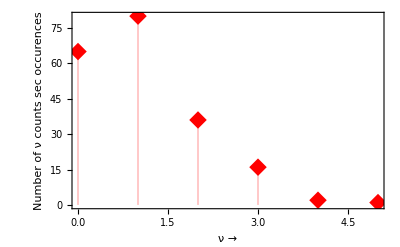

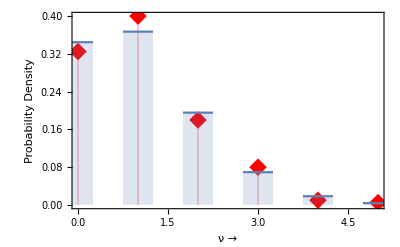

------------------------

Background, 50 sec (20hz) |  |  |  |  |  | 
# of measurements | Time, sec | Total Counts | Mean, counts | √Mean | σ | Rate, #/sec
1000 | 0.05 | 20 | 0.02±0.0045 | 0.141421 | 0.14007 | 0.4±0.089

# of counts | 0 | 1
Number of occurences getting # counts | 980 | 20
Probability Density | 0.98 | 0.02

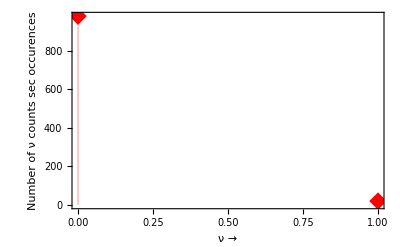

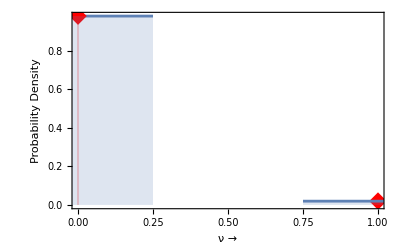

------------------------

------------------------

γ-decay, 50 sec (20Hz) |  |  |  |  |  | 
# of measurements | Time, sec | Total Counts | Mean, counts | √Mean | σ | Rate, #/sec
1000 | 0.05 | 815 | 0.815±0.029 | 0.902774 | 0.907523 | 16.3±0.57

# of counts | 0 | 1 | 2 | 3 | 4 | 5
Number of occurences getting # counts | 445 | 360 | 139 | 49 | 5 | 2
Probability Density | 0.445 | 0.36 | 0.139 | 0.049 | 0.005 | 0.002

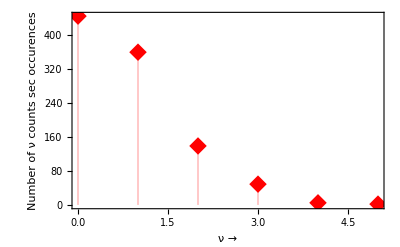

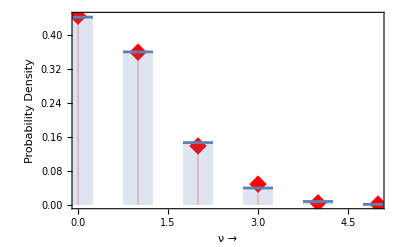

------------------------

------------------------

γ+β-decay, 50 sec (20Hz) |  |  |  |  |  | 
# of measurements | Time, sec | Total Counts | Mean, counts | √Mean | σ | Rate, #/sec
1000 | 0.05 | 21971 | 21.971±0.15 | 4.68732 | 3.63034 | 439.42±3.

# of counts | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 35
Number of occurences getting # counts | 1 | 10 | 12 | 32 | 62 | 54 | 79 | 95 | 130 | 106 | 98 | 88 | 77 | 45 | 40 | 24 | 18 | 13 | 9 | 2 | 3 | 2
Probability Density | 0.001 | 0.01 | 0.012 | 0.032 | 0.062 | 0.054 | 0.079 | 0.095 | 0.13 | 0.106 | 0.098 | 0.088 | 0.077 | 0.045 | 0.04 | 0.024 | 0.018 | 0.013 | 0.009 | 0.002 | 0.003 | 0.002

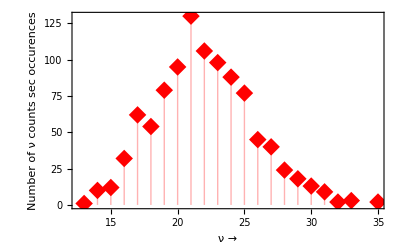

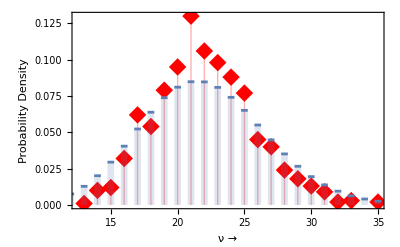

------------------------

------------------------

γ+β-decay, 10 sec (20Hz) |  |  |  |  |  | 
# of measurements | Time, sec | Total Counts | Mean, counts | √Mean | σ | Rate, #/sec
200 | 0.05 | 4375 | 21.875±0.33 | 4.67707 | 3.71191 | 437.5±6.6

# of counts | 12 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 32 | 34
Number of occurences getting # counts | 2 | 1 | 3 | 12 | 2 | 13 | 20 | 22 | 18 | 27 | 16 | 12 | 18 | 14 | 6 | 8 | 2 | 2 | 1 | 1
Probability Density | 0.01 | 0.005 | 0.015 | 0.06 | 0.01 | 0.065 | 0.1 | 0.11 | 0.09 | 0.135 | 0.08 | 0.06 | 0.09 | 0.07 | 0.03 | 0.04 | 0.01 | 0.01 | 0.005 | 0.005

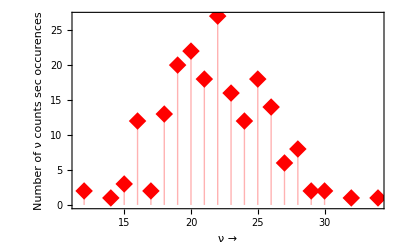

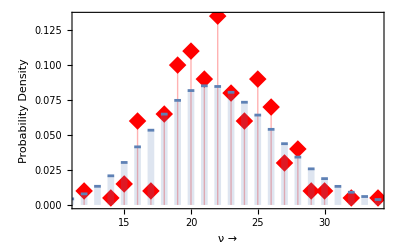

------------------------

------------------------

γ+β-decay, 10 sec (5Hz) |  |  |  |  |  | 
# of measurements | Time, sec | Total Counts | Mean, counts | √Mean | σ | Rate, #/sec
50 | 0.2 | 4333 | 86.66±1.3 | 9.30914 | 7.90404 | 433.3±6.6

# of counts | 70 | 73 | 74 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 90 | 91 | 92 | 93 | 94 | 95 | 97 | 98 | 102 | 105 | 106
Number of occurences getting # counts | 1 | 1 | 1 | 1 | 1 | 1 | 5 | 1 | 1 | 4 | 3 | 1 | 2 | 3 | 1 | 1 | 7 | 3 | 1 | 3 | 2 | 1 | 1 | 1 | 1 | 1 | 1
Probability Density | 0.02 | 0.02 | 0.02 | 0.02 | 0.02 | 0.02 | 0.1 | 0.02 | 0.02 | 0.08 | 0.06 | 0.02 | 0.04 | 0.06 | 0.02 | 0.02 | 0.14 | 0.06 | 0.02 | 0.06 | 0.04 | 0.02 | 0.02 | 0.02 | 0.02 | 0.02 | 0.02

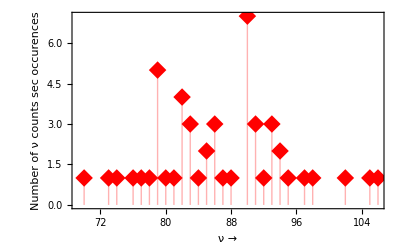

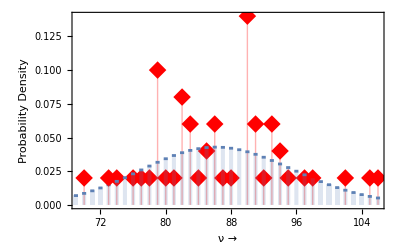

------------------------

```mathematica
(*var=bg50;*)
time20Hz=0.05; (* measurement time, in sec.*)
time5Hz = 0.2;

(* Length[var] is total # of measurements *)
(* Total[var] is Total # of Counts *)
(* Mean[var] is (Total # of Counts)/(# of measurements) *)
(* StandardDeviation[var] is σ for total # of measurements *)
(* Sqrt[Total[var]]/Length[var] is Uncertainty *)
(* Rate is Mean/time *)
(* Uncertainty for Rate is (Uncertainty for counts)/time *)
(* Tally counts the number of occurences getting # counts *)
(* Table[{N[Tally[var][[i,2]]/Length[var]]}, {i,Length[Tally[var]]}] is to calculate the probability  *)
(* PoissonDistribution[Mean[var]] calculates ⅇ^-μ μ^x/x!   *)

(*Grid[{{Text["γ-decay, 50 sec"],SpanFromLeft},{"# of measurements","Time, sec","Total Counts","Mean, counts","√Mean", "σ","Rate, #/sec"}, {Length[var], time, Total[var],  PlusMinus[N[Mean[var]],NumberForm[N[Sqrt[Total[var]]/Length[var]],2]],N[Sqrt[Mean[var]]], N[StandardDeviation[var]],PlusMinus[N[Mean[var]/time], NumberForm[Sqrt[Total[var]]/Length[var]/time,2]]}}, Frame -> All]
(* Grid[Transpose[Prepend[Sort[Table[{Tally[var][[i,1]],Tally[var][[i,2]],N[Tally[var][[i,2]]/Length[var]]}, {i,Length[Tally[var]]}]], {"# of counts", "Number of occurences getting # counts","Probability Density"}]], Frame -> All] *)
ListPlot[Tally[var], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, Frame->True,FrameLabel->{"ν →" ,"Number of ν counts sec occurences"}, PlotRange->All]
Show[ListPlot[Table[{Tally[var][[i,1]],N[Tally[var][[i,2]]/Length[var]]}, {i,Length[Tally[var]]}], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, PlotRange->All], DiscretePlot[PDF[PoissonDistribution[Mean[var]],k],{k,0,40},ExtentSize->{Scaled[.25], Scaled[.25]}, PlotRange->All], Frame->True,FrameLabel->{"ν →" ,"Probability Density"}]*)


"------------------------"
Grid[{{Text["Background, 50 sec (20hz)"],SpanFromLeft},{"# of measurements","Time, sec","Total Counts","Mean, counts","√Mean", "σ","Rate, #/sec"}, {Length[bg50], time20Hz, Total[bg50],  PlusMinus[N[Mean[bg50]],NumberForm[N[Sqrt[Total[bg50]]/Length[bg50]],2]],N[Sqrt[Mean[bg50]]], N[StandardDeviation[bg50]],PlusMinus[N[Mean[bg50]/time20Hz], NumberForm[Sqrt[Total[bg50]]/Length[bg50]/time20Hz,2]]}}, Frame -> All]

Grid[Transpose[Prepend[Sort[Table[{Tally[bg50][[i,1]],Tally[bg50][[i,2]],N[Tally[bg50][[i,2]]/Length[bg50]]}, {i,Length[Tally[bg50]]}]], {"# of counts", "Number of occurences getting # counts","Probability Density"}]], Frame -> All]
ListPlot[Tally[bg50], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, Frame->True,FrameLabel->{"ν →" ,"Number of ν counts sec occurences"}, PlotRange->All]

Show[ListPlot[Table[{Tally[bg50][[i,1]],N[Tally[bg50][[i,2]]/Length[bg50]]}, {i,Length[Tally[bg50]]}], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, PlotRange->All], DiscretePlot[PDF[PoissonDistribution[Mean[bg50]],k],{k,0,40},ExtentSize->{Scaled[.25], Scaled[.25]}, PlotRange->All], Frame->True,FrameLabel->{"ν →" ,"Probability Density"}]
"------------------------"

"------------------------"
Grid[{{Text["γ-decay, 50 sec (20Hz)"],SpanFromLeft},{"# of measurements","Time, sec","Total Counts","Mean, counts","√Mean", "σ","Rate, #/sec"}, {Length[down50], time20Hz, Total[down50],  PlusMinus[N[Mean[down50]],NumberForm[N[Sqrt[Total[down50]]/Length[down50]],2]],N[Sqrt[Mean[down50]]], N[StandardDeviation[down50]],PlusMinus[N[Mean[down50]/time20Hz], NumberForm[Sqrt[Total[down50]]/Length[down50]/time20Hz,2]]}}, Frame -> All]

Grid[Transpose[Prepend[Sort[Table[{Tally[down50][[i,1]],Tally[down50][[i,2]],N[Tally[down50][[i,2]]/Length[down50]]}, {i,Length[Tally[down50]]}]], {"# of counts", "Number of occurences getting # counts","Probability Density"}]], Frame -> All]

ListPlot[Tally[down50], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, Frame->True,FrameLabel->{"ν →" ,"Number of ν counts sec occurences"}, PlotRange->All]
Show[ListPlot[Table[{Tally[down50][[i,1]],N[Tally[down50][[i,2]]/Length[down50]]}, {i,Length[Tally[down50]]}], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, PlotRange->All], DiscretePlot[PDF[PoissonDistribution[Mean[down50]],k],{k,0,40},ExtentSize->{Scaled[.25], Scaled[.25]}, PlotRange->All], Frame->True,FrameLabel->{"ν →" ,"Probability Density"}]
"------------------------"

"------------------------"
Grid[{{Text["γ+β-decay, 50 sec (20Hz)"],SpanFromLeft},{"# of measurements","Time, sec","Total Counts","Mean, counts","√Mean", "σ","Rate, #/sec"}, {Length[up50], time20Hz, Total[up50],  PlusMinus[N[Mean[up50]],NumberForm[N[Sqrt[Total[up50]]/Length[up50]],2]],N[Sqrt[Mean[up50]]], N[StandardDeviation[up50]],PlusMinus[N[Mean[up50]/time20Hz], NumberForm[Sqrt[Total[up50]]/Length[up50]/time20Hz,2]]}}, Frame -> All]

Grid[Transpose[Prepend[Sort[Table[{Tally[up50][[i,1]],Tally[up50][[i,2]],N[Tally[up50][[i,2]]/Length[up50]]}, {i,Length[Tally[up50]]}]], {"# of counts", "Number of occurences getting # counts","Probability Density"}]], Frame -> All]

ListPlot[Tally[up50], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, Frame->True,FrameLabel->{"ν →" ,"Number of ν counts sec occurences"}, PlotRange->All]
Show[ListPlot[Table[{Tally[up50][[i,1]],N[Tally[up50][[i,2]]/Length[up50]]}, {i,Length[Tally[up50]]}], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, PlotRange->All], DiscretePlot[PDF[PoissonDistribution[Mean[up50]],k],{k,0,40},ExtentSize->{Scaled[.25], Scaled[.25]}, PlotRange->All], Frame->True,FrameLabel->{"ν →" ,"Probability Density"}]
"------------------------"

"------------------------"
Grid[{{Text["γ+β-decay, 10 sec (20Hz)"],SpanFromLeft},{"# of measurements","Time, sec","Total Counts","Mean, counts","√Mean", "σ","Rate, #/sec"}, {Length[up10Hz20], time20Hz, Total[up10Hz20],  PlusMinus[N[Mean[up10Hz20]],NumberForm[N[Sqrt[Total[up10Hz20]]/Length[up10Hz20]],2]],N[Sqrt[Mean[up10Hz20]]], N[StandardDeviation[up10Hz20]],PlusMinus[N[Mean[up10Hz20]/time20Hz], NumberForm[Sqrt[Total[up10Hz20]]/Length[up10Hz20]/time20Hz,2]]}}, Frame -> All]

Grid[Transpose[Prepend[Sort[Table[{Tally[up10Hz20][[i,1]],Tally[up10Hz20][[i,2]],N[Tally[up10Hz20][[i,2]]/Length[up10Hz20]]}, {i,Length[Tally[up10Hz20]]}]], {"# of counts", "Number of occurences getting # counts","Probability Density"}]], Frame -> All]

ListPlot[Tally[up10Hz20], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, Frame->True,FrameLabel->{"ν →" ,"Number of ν counts sec occurences"}, PlotRange->All]
Show[ListPlot[Table[{Tally[up10Hz20][[i,1]],N[Tally[up10Hz20][[i,2]]/Length[up10Hz20]]}, {i,Length[Tally[up10Hz20]]}], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, PlotRange->All], DiscretePlot[PDF[PoissonDistribution[Mean[up10Hz20]],k],{k,0,40},ExtentSize->{Scaled[.25], Scaled[.25]}, PlotRange->All], Frame->True,FrameLabel->{"ν →" ,"Probability Density"}]
"------------------------"

"------------------------"
Grid[{{Text["γ+β-decay, 10 sec (5Hz)"],SpanFromLeft},{"# of measurements","Time, sec","Total Counts","Mean, counts","√Mean", "σ","Rate, #/sec"}, {Length[up10Hz5], time5Hz, Total[up10Hz5],  PlusMinus[N[Mean[up10Hz5]],NumberForm[N[Sqrt[Total[up10Hz5]]/Length[up10Hz5]],2]],N[Sqrt[Mean[up10Hz5]]], N[StandardDeviation[up10Hz5]],PlusMinus[N[Mean[up10Hz5]/time5Hz], NumberForm[Sqrt[Total[up10Hz5]]/Length[up10Hz5]/time5Hz,2]]}}, Frame -> All]

Grid[Transpose[Prepend[Sort[Table[{Tally[up10Hz5][[i,1]],Tally[up10Hz5][[i,2]],N[Tally[up10Hz5][[i,2]]/Length[up10Hz5]]}, {i,Length[Tally[up10Hz5]]}]], {"# of counts", "Number of occurences getting # counts","Probability Density"}]], Frame -> All]

ListPlot[Tally[up10Hz5], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, Frame->True,FrameLabel->{"ν →" ,"Number of ν counts sec occurences"}, PlotRange->All]
Show[ListPlot[Table[{Tally[up10Hz5][[i,1]],N[Tally[up10Hz5][[i,2]]/Length[up10Hz5]]},{i,Length[Tally[up10Hz5]]}],PlotStyle->{Red},PlotMarkers->{"◆",18},Filling->Axis,PlotRange->All],DiscretePlot[PDF[PoissonDistribution[Mean[up10Hz5]],k],{k,0,Max[Tally[up10Hz5][[All,1]]]},ExtentSize->{Scaled[.25],Scaled[.25]},PlotRange->All],Frame->True,FrameLabel->{"ν →","Probability Density"}]
"------------------------"
```

The Physics and Calculations for each dataset share the same theoretical concepts.

The First Table for each of the datasets shows the
- The total # of measurements is the Length of each of Our datasets calculated by Length[var]
- Time, sec it the time interval between each of our measurements (Time Period = 1/frequency)
- Total Counts (calculated as Total[var]) is the total number of particles detected in the entire duration of the specific experimental run
- Mean is the average value of detections/measurement calculated as (Total # of Counts)/(# of measurements), (uncertainty in mean is calculated as Sqrt(mean/N) (SigmaBar - The std deviation of means within all possible subsets of the sample))
- σ = Sqrt( 1/(N-1)∑_(i=1)^N (x_i-x̄)^2) depicts how spread out our data is.
- The Rate, #/Second is the average expected detections per second calculated as the average (mean) Detections per measurement/time interval between measurements. (Simply Mean/Time)
- The uncertainty in the Rate is calculated as (Uncertainty for counts) / time or (As per Poisson Statistics Approximations) ((√_(Total Counts))/Length) / time.

The second Table for each dataset shows the
- Tally of all occurrences of getting a certain number of detections in a single measurement
- The probability distribution (density) depicts how likely we are to get certain detections within a certain interval of count interval
	Calculated in the software as Table[{N[Tally[var][[i, 2]]/Length[var]]}, {i, Length[Tally[var]]}]

The Plots:	
The first plot plots actual measurement tally for each #detections or number of occurrences getting # counts (as depicted by the second Table).
The Poisson distribution likely hood to get a certain value

The second plot overlays the probabilities calculated using the Poisson Distribution approximation for discrete datasets P(x, μ)=ⅇ^-μ μ^x/x over the actual frequency distribution as in plot one.

It can clearly be scene that when we have a smaller value of the mean, the Distribution is very skewed (simply because rare events are more likely to not occur than to occur). But as the mean value increases and the likelihood increases, the dataset gets closer to a Bell curve, showing a symmetrical distribution.

Step3.
- When does the histogram resemble a Gaussian curve centered on μ?
- On these histograms that can be approximated by a Gaussian distribution, overlay a Gaussian curve fit with proper parameters μ and σ on top of the histogram and Poisson distribution function.
If needed, check ‘Lab 1. Error Analysis I’ to see how to define and plot a Gaussian distribution. Include all the plotting functions inside one Show[...] function to overlay them on top of each other.
- Draw a vertical line on the histograms at the position of the mean. Show the range μ ± σ range on the histograms.
- Explain the relation of the counts observed in the experiment to the Poisson distribution. Also compare square roots of the means and standard deviations.
- Explain why the Poisson distribution can model the random behavior of the Cs-137 radioactive decay.

For a larger data set (which “seems” more continuous at surface), the histogram resembles a Gaussian curve centered on μ. I.e. datasets that detect γ+β-decay particles. This factor is there because practical datasets approach close resemblance to real datasets with greater sample space.
As explained earlier, a larger mean value is also a key factor into having a dataset seem closer to the gaussian curve. Lower mean value would mean a rare event, which in essence would be more likely to not occur than to occur. Hence, having a symmetry in the data is hard. As the mean value increases and the likelihood of the event increases, there seems to emerge a higher symmetry of the data about the mean value and hence, the data seems to more closely resemble the Gaussian Curve (The bell curve). This (as I would imagine) is the key that links the Poisson distribution to the Normal Distribution. Since the variance is mean, low mean values would mean a very skewed graph since it is all clumped besides the mean. With a high mean value however, there must be a high variance, and since the data is spread out, it is conna have a gradient like that in a bell curve. (if we think of a very high mean... the data would be centered about the mean value but spread across a very large area, exactly how a bell curve is!)

```mathematica
P[x_,  μ_, σ_]:=1/(√(2*π)*σ)*ⅇ^((-(x-μ)^2)/(2*(σ)^2));
PlotMyGaussian[dataset_] := Plot[P[x1, Mean[dataset], StandardDeviation[dataset]],{x1,Mean[dataset]-3.5 StandardDeviation[dataset],Mean[dataset]+3.5 StandardDeviation[dataset]},PlotRange->All, Frame->True];
```

```mathematica
(*------*)
```

```mathematica
"--------β+γ 50 seconds (20 Hz):--------"
Show[ListPlot[Table[{Tally[up50][[i,1]],N[Tally[up50][[i,2]]/Length[up50]]}, {i,Length[Tally[up50]]}], PlotStyle->{Red}, PlotMarkers->{"◆", 18}, Filling->Axis, PlotRange->All], DiscretePlot[PDF[PoissonDistribution[Mean[up50]],k],{k,0,40},ExtentSize->{Scaled[.25], Scaled[.25]}, PlotRange->All],
PlotMyGaussian[up50],
 Frame->True,FrameLabel->{"ν →" ,"Probability Density"}]
meanUp50=Mean[up50];
sigmaUp50 = StandardDeviation[up50];
N[meanUp50]
N[meanUp50+sigmaUp50]
N[meanUp50-sigmaUp50]
"--------β+γ 10 seconds (20 Hz):--------"
Show[ListPlot[Table[{Tally[up10Hz20][[i,1]],N[Tally[up10Hz20][[i,2]]/Length[up10Hz20]]},{i,Length[Tally[up10Hz20]]}],PlotStyle->{Red},PlotMarkers->{"◆",18},Filling->Axis,PlotRange->All],DiscretePlot[PDF[PoissonDistribution[Mean[up10Hz20]],k],{k,0,40},ExtentSize->{Scaled[.25],Scaled[.25]},PlotRange->All],
PlotMyGaussian[up10Hz20],Frame->True,FrameLabel->{"ν →","Probability Density"}]
meanUp10Hz20=Mean[up10Hz20];
sigmaUp10Hz20 = StandardDeviation[up10Hz20];
N[meanUp10Hz20]
N[meanUp10Hz20+sigmaUp10Hz20]
N[meanUp10Hz20-sigmaUp10Hz20]
"--------β+γ 10 seconds (5 Hz):--------"
Show[ListPlot[Table[{Tally[up10Hz5][[i,1]],N[Tally[up10Hz5][[i,2]]/Length[up10Hz5]]},{i,Length[Tally[up10Hz5]]}],PlotStyle->{Red},PlotMarkers->{"◆",18},Filling->Axis,PlotRange->All],DiscretePlot[PDF[PoissonDistribution[Mean[up10Hz5]],k],{k,0,Max[Tally[up10Hz5][[All,1]]]},ExtentSize->{Scaled[.25],Scaled[.25]},PlotRange->All],
PlotMyGaussian[up10Hz5],Frame->True,FrameLabel->{"ν →","Probability Density"}]
meanUp10Hz5=Mean[up10Hz5];
sigmaUp10Hz5 = StandardDeviation[up10Hz5];
N[meanUp10Hz5]
N[meanUp10Hz5+sigmaUp10Hz5]
N[meanUp10Hz5-sigmaUp10Hz5]
```

--------β+γ 50 seconds (20 Hz):--------

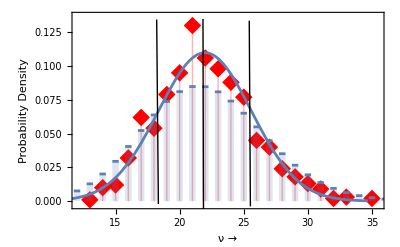

21.971

25.6013

18.3407

--------β+γ 10 seconds (20 Hz):--------

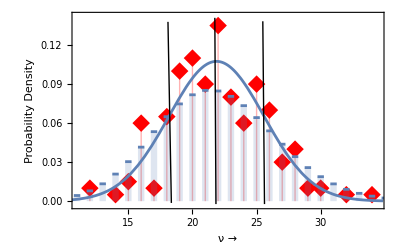

21.875

25.5869

18.1631

--------β+γ 10 seconds (5 Hz):--------

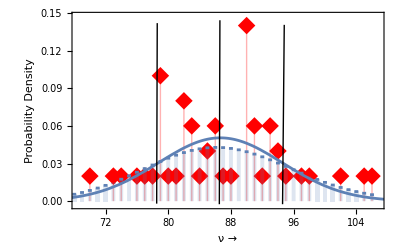

86.66

94.564

78.756

The Poisson Distribution can be seen to highly correlate with the actual data when the number of data-points is large (especially when the mean is very small). This is also when the Sqrt(mean) is very close to the standard deviation. As the sample space decreases and the mean value increases, the Poisson distribution doesn’t quite match the data-points as it does for a large number of low-valued data-points.

The Poisson distribution is used to model the probability of a certain number of DISCRETE events occurring in a fixed time interval when those events happen:

Randomly
Independently
At a predictable average rate (even if the individual events are random)

A radioactive decay shoots off discrete particles randomly, with each decay being independent. The overall decay rate is predictable (it is a 1st order reaction with a well known half-life). Hence, the Cs-137 radioactive decay has all the characteristics to be modelled by the Poisson distribution.

Step4.
- Collect and present all the calculations in one cumulative table with proper labels. Use Grid function. Write one row for each data set bg50, down50, .... To be able to show the numbers in correct format and with correct number of significant figures, use the functions, PlusMinus[a, b] which is a ± b, or Interval[a, b] which is the interval [a, b], and also check the functions ScientificForm, EngineeringForm, or NumberForm to write numbers with correct number of significant figures.
- Explain the difference between decay rates and their uncertainties in different runs. Explain statistical differences between results of the runs B and C; also between runs C, D, and E.
- Use error propagation rules for the errors and calculate the γ-decay rate and the β-decay rate of the radioactive source [do background subtraction]. Compare to the decay diagram above. Explain the discrepancy.

```mathematica
(*Function to show PlusMinus notation*)
PlusMinus[a_,b_]:=Row[{a," ± ",b}]

(*Define time intervals for 20Hz and 5Hz*)
time20Hz=1/20; (*Corresponding to 50ms or 20Hz*)
time5Hz=1/5;   (*Corresponding to 200ms or 5Hz*)

(*Grid structure for results table*)
Grid[{(*Headers for the table*){"Dataset","# of Measurements","Total Time (sec)","Total Counts","Mean Counts","Error in Mean (±)","Standard Deviation (σ)","Rate (#/sec)"},(*Data for bg50 (Background,50 sec at 20Hz)*){"Background, 50 sec (20Hz)",Length[bg50],Length[bg50]*time20Hz,Total[bg50],PlusMinus[NumberForm[N[Mean[bg50]],{5,2}],NumberForm[N[Sqrt[Total[bg50]]/Length[bg50]],{5,2}]],NumberForm[N[Sqrt[Mean[bg50]]],{5,2}],NumberForm[N[StandardDeviation[bg50]],{5,2}],PlusMinus[NumberForm[N[Mean[bg50]/time20Hz],{5,2}],NumberForm[N[Sqrt[Total[bg50]]/Length[bg50]/time20Hz],{5,2}]]},(*Data for down50 (Gamma decay,50 sec at 20Hz)*){"γ-decay, 50 sec (20Hz)",Length[down50],Length[down50]*time20Hz,Total[down50],PlusMinus[NumberForm[N[Mean[down50]],{5,2}],NumberForm[N[Sqrt[Total[down50]]/Length[down50]],{5,2}]],NumberForm[N[Sqrt[Mean[down50]]],{5,2}],NumberForm[N[StandardDeviation[down50]],{5,2}],PlusMinus[NumberForm[N[Mean[down50]/time20Hz],{5,2}],NumberForm[N[Sqrt[Total[down50]]/Length[down50]/time20Hz],{5,2}]]},(*Data for up50 (Gamma+Beta decay,50 sec at 20Hz)*){"γ+β-decay, 50 sec (20Hz)",Length[up50],Length[up50]*time20Hz,Total[up50],PlusMinus[NumberForm[N[Mean[up50]],{5,2}],NumberForm[N[Sqrt[Total[up50]]/Length[up50]],{5,2}]],NumberForm[N[Sqrt[Mean[up50]]],{5,2}],NumberForm[N[StandardDeviation[up50]],{5,2}],PlusMinus[NumberForm[N[Mean[up50]/time20Hz],{5,2}],NumberForm[N[Sqrt[Total[up50]]/Length[up50]/time20Hz],{5,2}]]},(*Data for up10Hz20 (Gamma+Beta decay,10 sec at 20Hz)*){"γ+β-decay, 10 sec (20Hz)",Length[up10Hz20],Length[up10Hz20]*time20Hz,Total[up10Hz20],PlusMinus[NumberForm[N[Mean[up10Hz20]],{5,2}],NumberForm[N[Sqrt[Total[up10Hz20]]/Length[up10Hz20]],{5,2}]],NumberForm[N[Sqrt[Mean[up10Hz20]]],{5,2}],NumberForm[N[StandardDeviation[up10Hz20]],{5,2}],PlusMinus[NumberForm[N[Mean[up10Hz20]/time20Hz],{5,2}],NumberForm[N[Sqrt[Total[up10Hz20]]/Length[up10Hz20]/time20Hz],{5,2}]]},(*Data for up10Hz5 (Gamma+Beta decay,10 sec at 5Hz)*){"γ+β-decay, 10 sec (5Hz)",Length[up10Hz5],Length[up10Hz5]*time5Hz,Total[up10Hz5],PlusMinus[NumberForm[N[Mean[up10Hz5]],{5,2}],NumberForm[N[Sqrt[Total[up10Hz5]]/Length[up10Hz5]],{5,2}]],NumberForm[N[Sqrt[Mean[up10Hz5]]],{5,2}],NumberForm[N[StandardDeviation[up10Hz5]],{5,2}],PlusMinus[NumberForm[N[Mean[up10Hz5]/time5Hz],{5,2}],NumberForm[N[Sqrt[Total[up10Hz5]]/Length[up10Hz5]/time5Hz],{5,2}]]}},Frame->All]
```

Dataset | # of Measurements | Total Time (sec) | Total Counts | Mean Counts | Error in Mean (±) | Standard Deviation (σ) | Rate (#/sec)
Background, 50 sec (20Hz) | 1000 | 50 | 20 | 0.02 ± 0.00 | 0.14 | 0.14 | 0.40 ± 0.09
γ-decay, 50 sec (20Hz) | 1000 | 50 | 815 | 0.81 ± 0.03 | 0.90 | 0.91 | 16.30 ± 0.57
γ+β-decay, 50 sec (20Hz) | 1000 | 50 | 21971 | 21.97 ± 0.15 | 4.69 | 3.63 | 439.42 ± 2.96
γ+β-decay, 10 sec (20Hz) | 200 | 10 | 4375 | 21.88 ± 0.33 | 4.68 | 3.71 | 437.50 ± 6.61
γ+β-decay, 10 sec (5Hz) | 50 | 10 | 4333 | 86.66 ± 1.32 | 9.31 | 7.90 | 433.30 ± 6.58

The Decay rates and their their uncertainties represent the number of particles expected to be detected per second. As expected, the background radioactivity measurements (A) have a very low (near zero) decay rate.

Since Gamma decay (B) is rare, it has a non-zero but still small decay rate.

C, D and E have similar decay rates that are very high as one would expect since they are measuring the radioactivity for both γ and β particles.

The uncertainty is related to both the decay rate itself and the Sample space. A smaller sample space giving lesser confidence. A Small decay rate would have a small uncertainty too (Even as per the Poisson distribution, this is true as std deviation = Sqrt(mean)).

Hence, A has low decay rate as well as uncertainty in the decay rate.
B has a relatively higher but still low decay rate with slightly higher uncertainty.
C has a much higher decay rate and uncertainty since it’s detecting both Beta and Gamma particles.
D and E have a lower sample space hence their uncertainty is even larger. The small differences in rates (between about 4 counts/sec) could be attributed to the shorter measurement time and increased statistical fluctuations in the lower count rates of runs D and E.
---
Overall, Differences Between B and C are experimental, they are dealing with completely different datasets as the rate and uncertainty suggest.

C, D and E have purely statistical differences in a sense that they deal with the same data - the same rate of β and γ particles but they do it over different intervals and sample rates. Hence, they have differences in their measurement. Although not much difference can be scene in case of C and D since the only thing that changes is the duration of the experiment; there is a notable difference when we get to E since a change is sample rate fundamentally means less  precision in the experiment.
---

γ-decay rate with background subtraction can be calculated as 
γ-decay rate (from experiment) - background radioactivity rate (from experiment) = 15.90 ± 0.66 counts/sec (error adds up while means subtract)

The β-decay rate can simply be calculated by subtracting off the value of the decay rate of the γ particles as well as any background radioactivity from our γ+β particle detection dataset decay rate.
I would take the dataset with the highest precision within our sample (C) since others have a smaller sample space.

Hence, the β-decay rate = (439.42 ± 2.96) - (15.90 ± 0.66) - (0.40 ± 0.09) = 423.12 ± 3.71 counts/sec

---
-Graphics-
Comparing this to the decay diagram, the diagram says that Cs137 always decays through a β decay but 94.6% of the time, the resulting particle is metastable.
85% of these would further get to the stable form through a γ decay.

Hence, for 100 β-decays, one would expect around 80 γ-decays. So the ratio of decay rates must be around 5/4.
But in our experiment, its around 26:1 !! Which is ver drastically different. I would guess this discrepancy is an issue with the apparatus. The apparatus may not detect all γ particles since they are so high energy that they would pass through a detector that is not efficient in collecting them (γ particles are more penetrating and might as well pass through the detector undetected.)

(researching a bit about Geiger Tubes, I realised this is one of the caveats of these detectors - they are much less efficient in detecting γ particles than detecting α and β particles.)

This explains the discrepancy of very fewer detections of γ particles.

Rutgers 275 Classical Physics Lab
“ERROR ANALYSIS II”
Contributed by Maryam Taherinejad and Girsh Blumberg ©2014